```mathematica
ω = Rectangle[{-l, 0}, {l, h1}]
```

Rectangle[{-l,0},{l,h1}]

```mathematica
leqn = Laplacian[ψ[z, y], {z,y}] == 0
```

ψ^(0,2)[z,y]+ψ^(2,0)[z,y]==0

```mathematica
bcond = {ψ[z,0]==-γ Zb, ψ[-l,y]==-γ Zs, ψ[l,y]==-γ Zs, (D[ψ[z,y], {y,1}] /. y->h1)==0}
```

{ψ[z,0]==-Zb γ,ψ[-l,y]==-Zs γ,ψ[l,y]==-Zs γ,ψ^(0,1)[z,h1]==0}

```mathematica
sol = DSolveValue[{leqn, bcond}, ϕ[z,y],{z,y}∈ω]//FullSimplify
```

DSolveValue[{ψ^(0,2)[z,y]+ψ^(2,0)[z,y]==0,{Zb γ+ψ[z,0]==0,Zs γ+ψ[-l,y]==0,Zs γ+ψ[l,y]==0,ψ^(0,1)[z,h1]==0}},{ⅇ^(-√k z) (ⅇ^(2 √k z) C[1]+C[2]) (C[1] Cos[√k y]+C[2] Sin[√k y])},{z,y}∈Rectangle[{-l,0},{l,h1}]]

```mathematica
ClearAll["Global`*"];
pde=Laplacian[ψ[x,y],{x,y}]==0;
bcLeft=Derivative[1,0][ψ][0,y]==0;
bcRight=ψ[l,y]==-γ*Zs;
bcTop=Derivative[0,1][ψ][x,h1]==0;
bcBottom=ψ[x,0]==-γ*Zb;
bc={bcLeft,bcRight,bcTop,bcBottom};
sol=DSolveValue[{pde,bc},ψ[x,y],{x,y},Assumptions->{0<=x<=l&&0<=y<=h1}]
ψtrue1[x,y]=ψ[x,y] /. sol
```

{{ψ[x,y]→(4 (-1)^K[1] Zb γ Cos[(π x (-1+2 K[1]))/(2 l)] Cosh[(π (h1-y) (-1+2 K[1]))/(2 l)] Sech[(h1 π (-1+2 K[1]))/(2 l)])/(-π+2 π K[1])K[1]1∞+-(4 Zs γ Cosh[(π x (-1+2 K[1]))/(2 h1)] Sech[(l π (-1+2 K[1]))/(2 h1)] Sin[(π y (-1+2 K[1]))/(2 h1)])/(-π+2 π K[1])K[1]1∞}}

{(4 (-1)^K[1] Zb γ Cos[(π x (-1+2 K[1]))/(2 l)] Cosh[(π (h1-y) (-1+2 K[1]))/(2 l)] Sech[(h1 π (-1+2 K[1]))/(2 l)])/(-π+2 π K[1])K[1]1∞+-(4 Zs γ Cosh[(π x (-1+2 K[1]))/(2 h1)] Sech[(l π (-1+2 K[1]))/(2 h1)] Sin[(π y (-1+2 K[1]))/(2 h1)])/(-π+2 π K[1])K[1]1∞}

```mathematica
m = 1000
λm=Pi * (2m-1)/(2l)
f1[x, y] = Cos[λm*x] * Cosh[λm*(h1-y)]*Sech[λm*h1] // FullSimplify
val = Sech[1999 Pi]
```

1000

(1999 π)/(2 l)

Cos[(1999 π x)/(2 l)] Cosh[(1999 π (h1-y))/(2 l)] Sech[(1999 h1 π)/(2 l)]

Sech[1999 π]

```mathematica
ClearAll["Global`*"];
pde=Laplacian[ψ[x,y],{x,y}]==0;
bcLeft=ψ[0,y]==-γ*Zs;
bcRight=ψ[(2*l),y]==-γ*Zs;
bcTop=ψ[x,(2*h1)]==-γ*Zb;
bcBottom=ψ[x,0]==-γ*Zb;
bc={bcLeft,bcRight,bcTop,bcBottom};
sol=DSolve[{pde,bc},ψ,{x,y},Assumptions->{0<=x<=(2*l)&&0<=y<=(2*h1)}] // FullSimplify
ψtrue2[x,y]=ψ[x+l,y] /. sol// FullSimplify
```

{{ψ→Function[{x,y},((2 Zs γ (-1+Cos[(π K[1])/Sign[h1]]) Csch[(l π K[1])/h1] Sin[(π y K[1])/(2 h1)] Sinh[(π (2 l-x) K[1])/(2 h1)])/(π K[1])+(2 Zs γ (-1+Cos[(π K[1])/Sign[h1]]) Csch[(l π K[1])/h1] Sin[(π y K[1])/(2 h1)] Sinh[(π x K[1])/(2 h1)])/(π K[1])+(2 Zb γ (-1+Cos[(π K[1])/Sign[l]]) Csch[(h1 π K[1])/l] Sin[(π x K[1])/(2 l)] Sinh[(π (2 h1-y) K[1])/(2 l)])/(π K[1])+(2 Zb γ (-1+Cos[(π K[1])/Sign[l]]) Csch[(h1 π K[1])/l] Sin[(π x K[1])/(2 l)] Sinh[(π y K[1])/(2 l)])/(π K[1]))K[1]1∞]}}

{-(4 γ (Zs Cosh[(π x K[1])/(2 h1)] Sech[(l π K[1])/(2 h1)] Sin[(π y K[1])/(2 h1)] Sin[(π K[1])/(2 Sign[h1])]^2+Zb Csch[(h1 π K[1])/l] Sin[(π (l+x) K[1])/(2 l)] Sin[(π K[1])/(2 Sign[l])]^2 (Sinh[(π (2 h1-y) K[1])/(2 l)]+Sinh[(π y K[1])/(2 l)])))/(π K[1])K[1]1∞}

```mathematica
SameQ[ψtrue1[x,y],ψtrue2[x,y]]
```

False

```mathematica
ϕ[z, y] = ({{(ⅇ^((√(1+De^2 k) z)/De) c1+ⅇ^(-(√(1+De^2 k) z)/De) c2) (c3 Cos[√k y]+c4 Sin[√k y])}})
Solve[ϕ[z, y]==Zb /. y==0 && -l<=z<=l, ϕ[z, y]==Zs /. z==-l && 0<y<h1,ϕ[z, y]==Zs /. z==l && 0<y<h1, ϕ[z, y]==Zint /. y==h1 && -l<=z<=l, {c1, c2, c3, c4}]
```

{(c2 ⅇ^(-(√(1+De^2 k) z)/De)+c1 ⅇ^((√(1+De^2 k) z)/De)) (c3 Cos[√k y]+c4 Sin[√k y])}

ReplaceAll::reps: {y==0&&-l≤z≤l} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {z==-l&&0<y<h1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {z==l&&0<y<h1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::nonopt: Options expected (instead of {c1,c2,c3,c4}) beyond position 4 in Solve[{(c2 Power[«2»]+c1 Power[«2»]) (c3 Cos[«1»]+c4 Sin[«1»])}==Zb/.y==0&&-l≤z≤l,{(c2 Power[«2»]+c1 Power[«2»]) (c3 Cos[«1»]+c4 Sin[«1»])}==Zs/.z==-l&&0<y<h1,{(c2 Power[«2»]+c1 Power[«2»]) (c3 Cos[«1»]+c4 Sin[«1»])}==Zs/.z==l&&0<y<h1,{(c2 Power[«2»]+c1 Power[«2»]) (c3 Cos[«1»]+c4 Sin[«1»])}==Zint/.y==h1&&-l≤z≤l,{c1,c2,c3,c4}]. An option must be a rule or a list of rules.

Solve[{(c2 ⅇ^(-(√(1+De^2 k) z)/De)+c1 ⅇ^((√(1+De^2 k) z)/De)) (c3 Cos[√k y]+c4 Sin[√k y])}==Zb/.y==0&&-l≤z≤l,{(c2 ⅇ^(-(√(1+De^2 k) z)/De)+c1 ⅇ^((√(1+De^2 k) z)/De)) (c3 Cos[√k y]+c4 Sin[√k y])}==Zs/.z==-l&&0<y<h1,{(c2 ⅇ^(-(√(1+De^2 k) z)/De)+c1 ⅇ^((√(1+De^2 k) z)/De)) (c3 Cos[√k y]+c4 Sin[√k y])}==Zs/.z==l&&0<y<h1,{(c2 ⅇ^(-(√(1+De^2 k) z)/De)+c1 ⅇ^((√(1+De^2 k) z)/De)) (c3 Cos[√k y]+c4 Sin[√k y])}==Zint/.y==h1&&-l≤z≤l,{c1,c2,c3,c4}]

InterpolatingFunction[…]

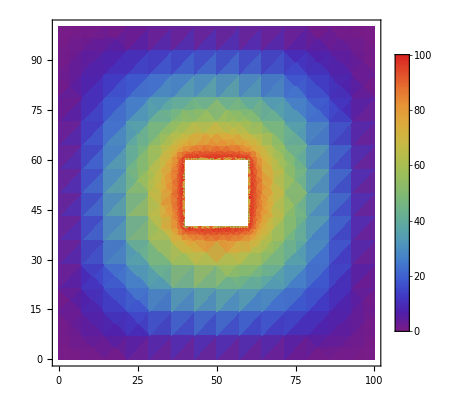

```mathematica
Ω=RegionDifference[Rectangle[{0,0},{100,100}],Rectangle[{40,40},{60,60}]];
sol=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==0,DirichletCondition[u[x,y]==100.,x==40&&40<=y<=60||x==60&&40<=y<=60||40<=x<=60&&y==40||40<=x<=60&&y==60],u[x,0]==u[x,100]==u[0,y]==u[100,y]==0},u,{x,y}∈Ω]

DensityPlot[sol[x,y],{x,y}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic]
```

```mathematica
D[f[x,y], {x,1}] /. x->1
```

f^(1,0)[1,y]